```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
Num =50;
Net= RandomGraph[BernoulliGraphDistribution[Num,0.4],DirectedEdges->True]
AdjM =  AdjacencyMatrix[Net];
```

-Graphics-

```mathematica
Total[AdjM[[1,All]]]
```

24

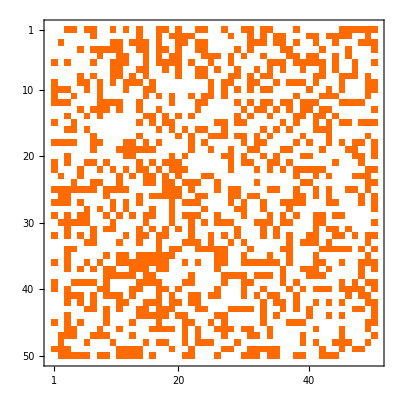

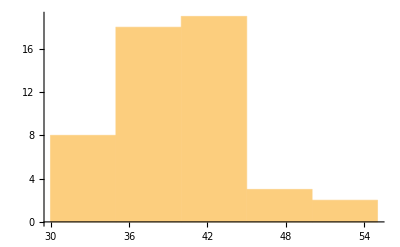

```mathematica
MatrixPlot[AdjM]
Histogram[VertexDegree[Net]]
```

```mathematica
(*Define percent adaptive foragers*)
F = 0.5;
G = Table[
rr=RandomReal[];
If[rr<F,
RandomVariate[UniformDistribution[{0.0,5}]],
0
],{i,1,Num}];
(*Randomly assign foraging efficiencies*)
f = Table[
If[i ≠ j,
RandomVariate[UniformDistribution[{0.0,1}]],
0
],{i,1,Num},{j,1,Num}];
(
(*Declare parameter values*)
r=0.8;
s=1;
e=0.1;
T = 100000;
(*Define population equations*)
eqnX = 
Table[{
Subscript[X, i]'[t] ==Subscript[X,i][t]*(r-s*Subscript[X,i][t] + Sum[AdjM[[i,j]]*e*f[[i,j]]*Subscript[a, i,j][t]* Subscript[X, j][t], {j,1,Num }]- Sum[AdjM[[j,i]]*f[[j,i]]*Subscript[a, j,i][t]* Subscript[X, j][t], {j,1,Num }])},{i,1,Num}];
(*Define foraging effort equations*)
eqnA = 
Table[{
Subscript[a, i,j]'[t] ==
AdjM[[i,j]]*(G[[i]]*Subscript[a, i,j][t] *(e*f[[i,j]]*Subscript[X,j][t] - Sum[AdjM[[i,k]]*Subscript[a, i,k][t]*e*f[[i,k]]*Subscript[X,k][t], {k,1,Num }]))},{i,1,Num},{j,1,Num}];
(*Declare starting conditions*)
startcond =Flatten[Join[{Table[Subscript[X, i][0]==RandomVariate[UniformDistribution[{0,0.1}]], {i,1, Num}],Table[Subscript[a, i,j][0]==AdjM[[i,j]]*(*RandomVariate[UniformDistribution[{0,1}]]*)10/Total[AdjM[[i,All]]], {i,1, Num},{j,1, Num}]}]];
(*Mathematica weirdness*)
varsX = Table[Subscript[X, i][t], {i,1, Num}];
varsA= Table[Subscript[a, i,j][t], {i,1, Num}, {j,1, Num}];
vars = Flatten[Join[varsX,{varsA}]];
eqns =Flatten[Join[eqnX,eqnA,startcond]];
(*This step solves the equations*)
sol=NDSolve[eqns, vars, {t,1,T}];
)//Timing
```

{4.83343,Null}

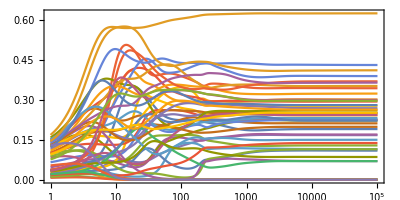

```mathematica
(*Plot Populations over time*)
LogLinearPlot[Evaluate[varsX/.sol],{t,1,T},AxesOrigin->{0,0},AspectRatio->0.5,PlotRange->All,Frame->True]
```

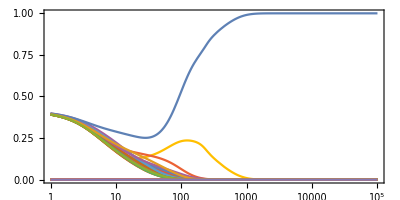

```mathematica
(*Plot foraging effort for species i*)
i=12;
LogLinearPlot[Evaluate[varsA[[i,All]]/.sol],{t,1,T},AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->All,Frame->True]
```